```mathematica
Quit[];
```

```mathematica
data = {{1,913.5714285714286},{2,886.7142857142857},{3,860.2857142857143},{4,878.5714285714286},{5,877.8571428571429},{6,834.7142857142857},{7,844.7142857142857},{8,805.8571428571429},{9,794.7142857142857},{10,763.1428571428571},{11,725.5714285714286},{12,719.5714285714286},{13,712.0},{14,674.0},{15,642.2857142857143},{16,627.2857142857143},{17,620.1428571428571},{18,589.2857142857143},{19,568.4285714285714},{20,549.1428571428571},{21,533.0},{22,493.7142857142857},{23,487.0},{24,475.85714285714283},{25,466.42857142857144},{26,444.2857142857143},{27,428.42857142857144},{28,393.85714285714283},{29,411.2857142857143},{30,397.2857142857143},{31,390.14285714285717},{32,378.42857142857144},{33,359.7142857142857},{34,346.85714285714283}}
```

{{1,913.571},{2,886.714},{3,860.286},{4,878.571},{5,877.857},{6,834.714},{7,844.714},{8,805.857},{9,794.714},{10,763.143},{11,725.571},{12,719.571},{13,712.},{14,674.},{15,642.286},{16,627.286},{17,620.143},{18,589.286},{19,568.429},{20,549.143},{21,533.},{22,493.714},{23,487.},{24,475.857},{25,466.429},{26,444.286},{27,428.429},{28,393.857},{29,411.286},{30,397.286},{31,390.143},{32,378.429},{33,359.714},{34,346.857}}

```mathematica
line = Fit[data, {1, x, x^2}, x]
```

962.24-22.6839 x+0.12239 x^2

```mathematica
F[x_] =line
```

962.24-22.6839 x+0.12239 x^2

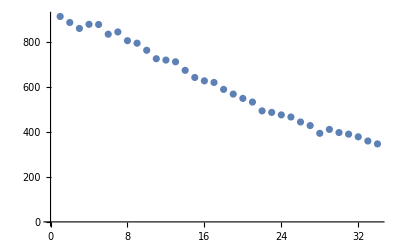

```mathematica
plt1 = Plot[F[x], {x, 1, 100}, PlotRange->{0, 1000}];
plt2 = ListPlot[data];
```

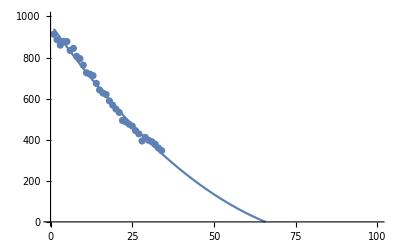

```mathematica
Show[plt1, plt2]
```

```mathematica
Solve[F[x] == 0, x]
```

{{x→65.7308},{x→119.61}}

```mathematica
Integrate[F[x], {x, 34, 66}]
```

4622.85